```mathematica
SetDirectory["/Users/naomi/Projects"]
```

/Users/naomi/Projects

```mathematica
Get["QSIM/QSIM_basicFunctions.m"]
Get["QSIM/QSIM_measurement.m"]
Get["QSIM/QSIM_stabilizers.m"]
Get["QSIM/QSIM_nonlocal.m"]
Get["QSIM/QSIM_noise.m"]
Get["QSIM/QSIM_superoperators.m"]
Get["QSIM/QSIM_errorAnalysis.m"]
```

```mathematica
rot[θ_]:=Cos[θ/2]*id-I*Sin[θ/2]*pY
```

```mathematica
proj[θ_]:=CT[rot[θ]].projEvenMatrix[1].rot[θ]
```

```mathematica
Module[{state,s,ss,p,nSamples,measureState,eval,evec,z1,peven,podd,ypeven,ypodd,fidelities},

nSamples = 100;
ss=RandomVariate[NormalDistribution[0,0.5],nSamples];
measureState =phi0;
z1=KP[pZ,id];

For[i=1,i<nSamples,i++,
s = ss⟦i⟧;
state = phi0;
p=KP[ proj[s],id];
state = p.state.CT[p];

If[Random[]<0.5, state = z1.state.CT[z1]];

measureState=measureState+state;


];

measureState = measureState/Tr[measureState];

{eval,evec}=createSuperoperator[measureState];
Print@eval;
Fidelity[projEvenMatrix[1],#]&/@evec;
Fidelity[projOddMatrix[1],#]&/@evec;
Chop@Fidelity[I*pY.projEvenMatrix[1],#]&/@evec;

Chop@Fidelity[I*pY.projOddMatrix[1],#]&/@evec;

(* Find ideal superoperators and test against the one found *)

peven = KP[projEvenMatrix[1],id].phi0. KP[projEvenMatrix[1],id];
podd =KP[projOddMatrix[1],id].phi0. KP[projOddMatrix[1],id];
ypeven =KP[pY.projEvenMatrix[1],id].phi0.CT[KP[pY.projEvenMatrix[1],id]];
ypodd =KP[pY.projOddMatrix[1],id].phi0.CT[KP[pY.projOddMatrix[1],id]];

fidelities=2*Fidelity[#,measureState]&/@{peven,podd,ypeven,ypodd};
Print@fidelities;
Print@(1-Plus@@fidelities)

]
```

{0.888052,0.057489,0.0366793,0.0177798}

{0.887294,0.0181175,0.0472944,0.0472944}

-2.22045×10^-16

```mathematica
?Fidelity
```

"Fidelity[ρ_1,ρ_2] gives the fidelity of two density matrices "

```mathematica
sol1=Integrate[PDF[NormalDistribution[0,Ω],θ]*Cos[θ/2]^4,{θ,-Pi,Pi}]
```

1/16 (6 Erf[π/(√2 Ω)]+ⅇ^(-2 Ω^2) (4 ⅇ^((3 Ω^2)/2) (Erf[(π-ⅈ Ω^2)/(√2 Ω)]+Erf[(π+ⅈ Ω^2)/(√2 Ω)])+Erf[(π-2 ⅈ Ω^2)/(√2 Ω)]+Erf[(π+2 ⅈ Ω^2)/(√2 Ω)]))

```mathematica
sol2=Integrate[PDF[NormalDistribution[0,Ω],θ]*Sin[θ/2]^4,{θ,-Pi,Pi}]
```

1/16 (6 Erf[π/(√2 Ω)]+ⅇ^(-2 Ω^2) (-4 ⅇ^((3 Ω^2)/2) (Erf[(π-ⅈ Ω^2)/(√2 Ω)]+Erf[(π+ⅈ Ω^2)/(√2 Ω)])+Erf[(π-2 ⅈ Ω^2)/(√2 Ω)]+Erf[(π+2 ⅈ Ω^2)/(√2 Ω)]))

```mathematica
sol3=Integrate[PDF[NormalDistribution[0,Ω],θ]*Sin[θ/2]^2*Cos[θ/2]^2,{θ,-Pi,Pi}]
```

1/16 (2 Erf[π/(√2 Ω)]+ⅇ^(-2 Ω^2) (-2+Erfc[(π-2 ⅈ Ω^2)/(√2 Ω)]+Erfc[(π+2 ⅈ Ω^2)/(√2 Ω)]))

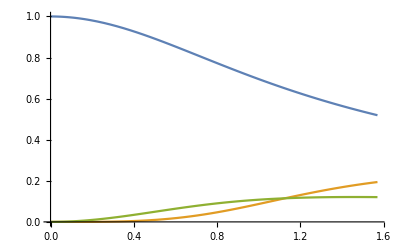

```mathematica
Plot[{sol1,sol2,sol3},{Ω,0,Pi/2}]
```

```mathematica
Erfc
```

(ⅇ^(-θ^2/(2 Ω^2)))/(√(2 π) Ω)